Pure Anonymous Functions

After all the examples we’ve seen of the Wolfram Language, we’re now ready to go to a slightly higher level of abstraction, and tackle the very important concept of pure functions (also known as pure anonymous functions).

Using pure functions will let us unlock a new level of power in the Wolfram Language, and also let us redo some of the things we’ve done before in a simpler and more elegant way.

Let’s start with a simple example. Say we’ve got a list of images, and we want to apply Blur to each of them. That’s easy to do with /@.

Apply Blur to each image in the list:

```mathematica
Blur/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

But now let’s say we want to include the parameter 5 in Blur. How can we do that? The answer is to use a pure function.

Include a parameter by introducing a pure function:

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

The original blur written as a pure function:

```mathematica
Blur[#]&/@{-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-}

The # is a “slot” into which each element is put. The & says that what comes before it is a pure function.

Here’s the equivalent of Blur[#,5]&/@... expanded out:

```mathematica
{Blur[-Graphics-,5],Blur[-Graphics-,5],Blur[-Graphics-,5]}
```

{-Graphics-,-Graphics-,-Graphics-}

Let’s look at some other examples. Every time, the slot indicates where to put each element when the pure function is applied.

Rotate each string by 90°:

```mathematica
Rotate[#,90Degree]&/@{"one","two","three"}
```

{one,two,three}

Take a string and rotate it different amounts:

```mathematica
Rotate["hello",#]&/@{30°,90°,180°,220°}
```

{hello,hello,hello,hello}

Show text in a list of different colors:

```mathematica
Style["hello",20,#]&/@{Red,Orange,Blue,Purple}
```

{hello,hello,hello,hello}

Make circles different sizes:

```mathematica
Graphics[Circle[ ],ImageSize->#]&/@{20,40,30,50,10}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Show framed columns of a color and its negation:

```mathematica
Framed[Column[{#,ColorNegate[#]}]]&/@{Red,Green,Blue,Purple,Orange}
```

{RGBColor[1, 0, 0]
RGBColor[0., 1., 1.],RGBColor[0, 1, 0]
RGBColor[1., 0., 1.],RGBColor[0, 0, 1]
RGBColor[1., 1., 0.],RGBColor[0.5, 0, 0.5]
RGBColor[0.5, 1., 0.5],RGBColor[1, 0.5, 0]
RGBColor[0., 0.5, 1.]}

Compute the lengths of three Wikipedia articles:

```mathematica
StringLength[WikipediaData[#]]&/@{"apple","peach","pear"}
```

{31045,24153,11115}

Pair topics with results:

```mathematica
{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}
```

{{apple,31045},{peach,24153},{pear,11115}}

Make a grid of everything:

```mathematica
Grid[{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}]
```

apple | 31045
peach | 24153
pear | 11115

This makes a list of digits, then maps a pure function over it:

```mathematica
Style[#,Hue[#/10],5*#]&/@IntegerDigits[2^100]
```

{1,2,6,7,6,5,0,6,0,0,2,2,8,2,2,9,4,0,1,4,9,6,7,0,3,2,0,5,3,7,6}

Here’s what the pure function would do if mapped over {6,8,9}:

```mathematica
{Style[6,Hue[6/10],5*6],Style[8,Hue[8/10],5*8],Style[9,Hue[9/10],5*9]}
```

{6,8,9}

Now that we’ve seen some examples of pure functions in action, let’s look more abstractly at what’s going on.

This maps an abstract pure function over a list:

```mathematica
f[#,x]&/@{a,b,c,d,e}
```

{f[a,x],f[b,x],f[c,x],f[d,x],f[e,x]}

Here’s the minimal example:

```mathematica
f[#]&/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

It’s equivalent to:

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[b],f[c],f[d],f[e]}

We can put slots wherever we want in the pure function, as many times as we want. All the slots will get filled with whatever the pure function is applied to.

Apply a slightly more complicated pure function:

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}
```

{f[a,{x,a},{a,a}],f[b,{x,b},{b,b}],f[c,{x,c},{c,c}]}

It’s easier to read in a column:

```mathematica
f[#,{x,#},{#,#}]&/@{a,b,c}//Column
```

f[a,{x,a},{a,a}]
f[b,{x,b},{b,b}]
f[c,{x,c},{c,c}]

OK, now we’re ready to finally discuss how pure functions really work. When we write f[x], we’re applying the function f to x. Often we’ll use a specific named function instead of f, say Blur, so we have Blur[x], etc.

But the point is that we can also replace f with a pure function. Then whatever we apply this to will be used to fill the slot in the pure function.

Apply a pure function to x, so the # slot gets filled with x:

```mathematica
f[#,a]&  [x]
```

f[x,a]

An equivalent form, written with @ instead of [ ... ]:

```mathematica
f[#,a]& @ x
```

f[x,a]

So now we can see what /@ is doing: it’s just applying the pure function to each element in the list.

```mathematica
f[#,a]&/@{x,y,z}
```

{f[x,a],f[y,a],f[z,a]}

The same thing, written out more explicitly:

```mathematica
{f[#,a]& @ x, f[#,a]& @ y, f[#,a]& @ z}
```

{f[x,a],f[y,a],f[z,a]}

Why is this useful? First of all, because it’s the foundation for all the things pure functions do with /@. But it’s actually also often useful on its own, for example as a way to avoid having to repeat things.

Here’s an example of a pure function involving three occurrences of #.

Apply a pure function to Blend[{Red,Yellow}]:

```mathematica
Column[{#,ColorNegate[#],#}]& [Blend[{Red,Yellow}]]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

This is what it looks like without the pure function:

```mathematica
Column[{Blend[{Red,Yellow}],ColorNegate[Blend[{Red,Yellow}]],Blend[{Red,Yellow}]}]
```

RGBColor[1, Rational[1, 2], 0]
RGBColor[0., 0.5, 1.]
RGBColor[1, Rational[1, 2], 0]

In the Wolfram Language, a pure function works just like anything else. On its own, though, it doesn’t do anything.

Enter a pure function on its own and it’ll come back unchanged:

```mathematica
f[#,2]&
```

f[#1,2]&

Give it to the function Map (/@), though, and it’ll be used to do a computation.

Map uses the pure function to do a computation:

```mathematica
Map[f[#,2]&,{a,b,c,d,e}]
```

{f[a,2],f[b,2],f[c,2],f[d,2],f[e,2]}

Over the course of the next few sections, we’ll see more and more uses of pure functions.

Vocabulary

code& |   | a pure function 
# |   | slot in a pure function

"8 Exercises Available"
"with 1 extras" | "Get Started »"

Use Range and a pure function to create a list of the first 20 squares. »

| Expected output: |  
  | {1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400} |

Make a list of the result of blending yellow, green and blue with red. »

| Expected output: |  
  | {RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]} |

Generate a list of framed columns containing the uppercase and lowercase versions of each letter of the alphabet. »

| Expected output: |  
  | {"A"
"a","B"
"b","C"
"c","D"
"d","E"
"e","F"
"f","G"
"g","H"
"h","I"
"i","J"
"j","K"
"k","L"
"l","M"
"m","N"
"n","O"
"o","P"
"p","Q"
"q","R"
"r","S"
"s","T"
"t","U"
"u","V"
"v","W"
"w","X"
"x","Y"
"y","Z"
"z"} |

Make a list of letters of the alphabet, in random colors, with frames having random background colors. »

| Sample expected output: |  
  | {"a","b","c","d","e","f","g","h","i","j","k","l","m","n","o","p","q","r","s","t","u","v","w","x","y","z"} |

Make a table of G5 countries, together with their flags, and arrange the result in a fully framed grid. »






| Expected output: |  
  | "France" | -Graphics-
"Germany" | -Graphics-
"Japan" | -Graphics-
"United Kingdom" | -Graphics-
"United States" | -Graphics- |

Make a list of word clouds for the Wikipedia articles about apple, peach and pear. »

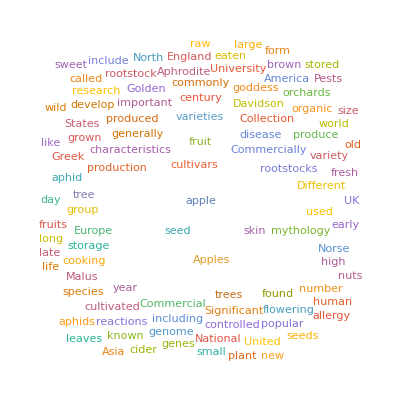
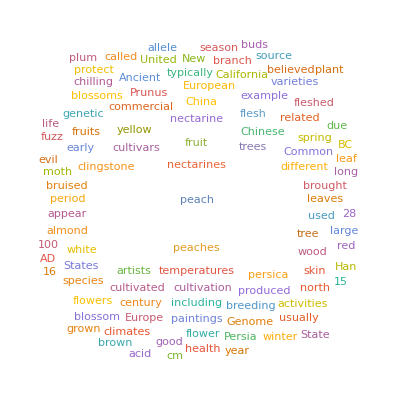
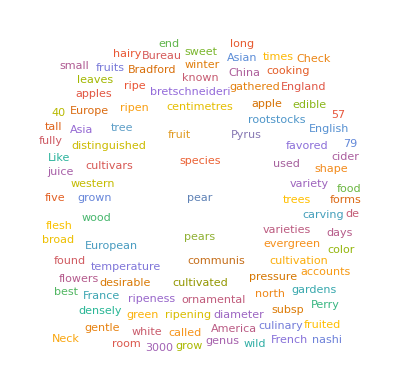
| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Make a list of histograms of the word lengths in Wikipedia articles on apple, peach and pear. »

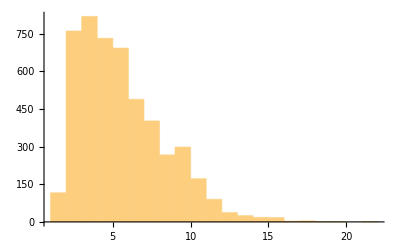
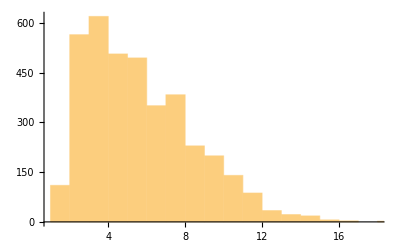
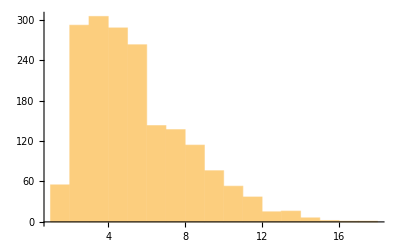
| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-} |

Make a list of maps of Central America, highlighting each country in turn. »

| Expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Give a simpler form for (#^2+1&)/@Range[10]. »

| Expected output: |  
  | {2,5,10,17,26,37,50,65,82,101} |

Q&A

Why are they called “pure functions”?

Because all they do is serve as functions that can be applied to arguments. They’re also sometimes called anonymous functions, because, unlike say Blur, they’re not referred to by a name. Here I’m calling them “pure anonymous functions” to communicate both meanings.

Why does one need the &?

The &(ampersand) indicates that what comes before it is the “body” of a pure function, not the name of a function.  f/@{1,2,3} gives {f[1],f[2],f[3]}but f&/@{1,2,3}  gives {f,f,f}.

What is f[#,1]& interpreted as?

Function[f[#,1]]. The Function here is sometimes called the “function function”.

Tech Notes

Pure functions are a characteristic feature of functional programming. They’re often called lambda expressions, after their use in mathematical logic in the 1930s. Confusingly, the term “pure function” sometimes just means a function that has no side effects (i.e. assigns no values to variables, etc.)

Table[f[x],{x,{a,b,c}}] actually does the same as f/@{a,b,c}. It’s sometimes useful, particularly if one doesn’t want to have to explain pure functions.

Be careful if you have multiple nested &’s in an expression! Sometimes you may have to insert parentheses. And sometimes you may have to use Function with a named variable, as in Function[x,x^2] rather than #^2&, to avoid conflicts between uses of # in different functions.

It sometimes makes for good-looking code to write Function[x,x^2] as x↦x^2. The ↦ is automatically constructed when you type the three characters |->. A form like x ↦x^2 coincides with the standard mathematical notation for “x is mapped to x^2” or “x becomes x^2”.

Options can often be pure functions. It’s important to put parentheses around the whole pure function, as in ColorFunction→(Hue[#/4]&), or it won’t be interpreted as you expect.

There are elegant ways to avoid having to explicitly use # and &. Much as  f is equivalent to  f[#]&,  f@*g (discussed in Section 45) is equivalent to  f[g[#]]&. OperatorApplied[f][y] is equivalent to  f[#,y]& etc.

More to Explore

Guide to Functional Programming in the Wolfram Language »